```mathematica
Animate[Plot[Exp[-(t-x/1)^2],{x,-5,5},PlotRange->{-2,2},PlotStyle->Thick],{t,-7,7},AnimationRunning->False]
```

```mathematica
Animate[Plot[(-1)Exp[-(t+x/1)^2],{x,-5,5},PlotRange->{-2,2},PlotStyle->Thick],{t,-7,7},AnimationRunning->False]
```

```mathematica
Animate[Plot[{(Exp[-(t-x/1)^2]+(-1)Exp[-(t+x/1)^2])(*,Exp[-(t-x/1)^2],(-1)Exp[-(t+x/1)^2]*)},{x,-5,5},PlotRange->{-2,2},PlotStyle->Thick],{t,-7,7},AnimationRunning->True]
```

```mathematica
Animate[Plot[{(UnitStep[t-x]-UnitStep[t-x-2]+(-1)(UnitStep[t+x]-UnitStep[t+x-2]))(*,(UnitStep[t-x]-UnitStep[t-x-2]),(-1)(UnitStep[t+x]-UnitStep[t+x-2])*)},{x,-5,5},PlotRange->{-2,2},PlotStyle->Thick,ExclusionsStyle->Automatic],{t,-6,6},AnimationRunning->True]
```

```mathematica
Animate[Plot[(Cos[5x+π t]((UnitStep[t-x]-UnitStep[t-x-π])+(-1)(UnitStep[t+x]-UnitStep[t+x-π]))),{x,-10,0},PlotRange->{-2,2},PlotStyle->Thick],{t,-5,10}]
```

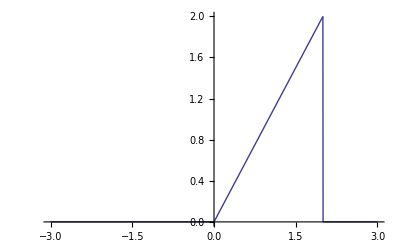

```mathematica
Plot[x(( UnitStep[x]-UnitStep[x-1]-(-UnitStep[x-1]+UnitStep[x-2]))),{x,-3,3},ExclusionsStyle->Automatic]
```